# HW #5: 4.1 CE’s # 2, 11, 17 4.2 # 1, 6, 7, 8, 17

## Cole Pendergraft

Code for computing dividedDifference tables and newtonForm polynomials:

```mathematica
dividedDifference[t_]:=
Module[{m,xData,yData,n},(*We'll locally hold a matrix, the x,y data, and the length of t*)
n=Length[t]; (*Indexing is always confusing, this "should be" n+1, but bear with me*)
m=Table[0,{n},{n}]; (*This is where the table will live*)
xData=Transpose[t][[1]];yData=Transpose[t][[2]]; (*grab the x's and y's*)
m[[1]]=yData; m=Transpose[m]; (*The first column of dd's is the y-values*)
For[col=2,col≤n,col++,(*First iterate through columns*)
For[entry=col,entry≤n,entry++,(*In a column, start at the diagonal and iterate DOWN*)
m[[entry]][[col]]=(m[[entry]][[col-1]]-m[[entry-1]][[col-1]])/(xData[[entry]]-xData[[entry-col+1]])
(*The indexing is tricky, and would be easier if the first column was the "0" column*)]
];
Return[m]]
```

```mathematica
newtonForm[t_]:=
Module[{coeffs,xData, sum,prod,n},(*We'll need to grab the xData again for the roots, and then keep a table of coefficients*)
n=Length[t];xData=Transpose[t][[1]];
coeffs=Diagonal[dividedDifference[t]];Print["List of coefficients:",coeffs];sum=coeffs[[1]];(*Initialize with the constant term*)
prod=1;
For[term=1,term<n,term++,(*Remember, we're building a degree n-1 poly*)
prod*=(x-xData[[term]]);
sum+=coeffs[[term+1]]*prod (*1st coefficient is already there, so we're going from 2 to n*)
];
Return[sum];
]
```

## 4.1 CE # 2

Find the polynomial of degree 10 that interpolates the function arctan(x) at 11 equally spaced points in the interval [1, 6]. Print the coefficients in the Newton form of the polynomial. Compute and print the difference between the polynomial and the function at 33 equally spaced points in the interval [0, 8]. What conclusion can  be drawn?

Creating a data table of 10 values between x = [1, 6]:

```mathematica
Clear[data1];
Clear[f];

f[x_] = ArcTan[x];
data1 = Table[{.5i, f[.5i]}, {i, 2, 12}]
```

{{1.,0.785398},{1.5,0.982794},{2.,1.10715},{2.5,1.19029},{3.,1.24905},{3.5,1.2925},{4.,1.32582},{4.5,1.35213},{5.,1.3734},{5.5,1.39094},{6.,1.40565}}

Creating interpolation polynomial of degree 10. I also modified the newtonForm code so that it prints out our list of coefficients:

```mathematica
Clear[p];
p[x_] = newtonForm[data1]
```

List of coefficients:{0.785398,0.394791,-0.146081,0.0424357,-0.00999897,0.00193349,-0.000302948,0.0000359312,-2.27132×10^-6,-2.85027×10^-7,1.37917×10^-7}

0.785398+0.394791 (-1.+x)-0.146081 (-1.5+x) (-1.+x)+0.0424357 (-2.+x) (-1.5+x) (-1.+x)-0.00999897 (-2.5+x) (-2.+x) (-1.5+x) (-1.+x)+0.00193349 (-3.+x) (-2.5+x) (-2.+x) (-1.5+x) (-1.+x)-0.000302948 (-3.5+x) (-3.+x) (-2.5+x) (-2.+x) (-1.5+x) (-1.+x)+0.0000359312 (-4.+x) (-3.5+x) (-3.+x) (-2.5+x) (-2.+x) (-1.5+x) (-1.+x)-2.27132×10^-6 (-4.5+x) (-4.+x) (-3.5+x) (-3.+x) (-2.5+x) (-2.+x) (-1.5+x) (-1.+x)-2.85027×10^-7 (-5.+x) (-4.5+x) (-4.+x) (-3.5+x) (-3.+x) (-2.5+x) (-2.+x) (-1.5+x) (-1.+x)+1.37917×10^-7 (-5.5+x) (-5.+x) (-4.5+x) (-4.+x) (-3.5+x) (-3.+x) (-2.5+x) (-2.+x) (-1.5+x) (-1.+x)

And now we can just confirm that what we have actually is a polynomial of degree 10:

```mathematica
Simplify[p[x]]
```

-0.105316+1.45162 x-0.773588 x^2+0.257511 x^3-0.0469661 x^4+0.000592218 x^5+0.00201611 x^6-0.000535462 x^7+0.0000695556 x^8-4.76732×10^-6 x^9+1.37917×10^-7 x^10

Now we can print the error values between each  calculation on the 33 values in [0, 8]:

```mathematica
Clear[data2];
Clear[Er];
Er[x_] = (Abs[p[x] - f[x]]); (* Just a simple function for computing the error between Arctan[x] and the Interpolating Polynomial we generated *)
data2 = MatrixForm[Table[{.242424i, p[.242424i], f[.242424i], Er[.242424i]}, {i, 0, 33}]]
```

(0. | -0.105316 | 0. | 0.105316
0.242424 | 0.204635 | 0.237836 | 0.0332003
0.484848 | 0.443439 | 0.451453 | 0.00801336
0.727272 | 0.627521 | 0.628796 | 0.00127491
0.969696 | 0.76998 | 0.770014 | 0.000034523
1.21212 | 0.881037 | 0.880996 | 0.0000410831
1.45454 | 0.968512 | 0.968509 | 3.63205×10^-6
1.69697 | 1.03829 | 1.03829 | 4.52845×10^-6
1.93939 | 1.09473 | 1.09473 | 7.76308×10^-7
2.18182 | 1.14103 | 1.14103 | 9.48503×10^-7
2.42424 | 1.17956 | 1.17956 | 2.69021×10^-7
2.66666 | 1.21203 | 1.21203 | 3.19358×10^-7
2.90909 | 1.2397 | 1.2397 | 1.3867×10^-7
3.15151 | 1.26354 | 1.26354 | 1.60052×10^-7
3.39394 | 1.28426 | 1.28426 | 1.02139×10^-7
3.63636 | 1.30243 | 1.30243 | 1.15036×10^-7
3.87878 | 1.31848 | 1.31848 | 1.05969×10^-7
4.12121 | 1.33275 | 1.33275 | 1.17163×10^-7
4.36363 | 1.34552 | 1.34552 | 1.55893×10^-7
4.60606 | 1.35701 | 1.35701 | 1.70934×10^-7
4.84848 | 1.3674 | 1.3674 | 3.35489×10^-7
5.0909 | 1.37684 | 1.37684 | 3.72123×10^-7
5.33333 | 1.38545 | 1.38545 | 1.13535×10^-6
5.57575 | 1.39333 | 1.39333 | 1.33583×10^-6
5.81818 | 1.40058 | 1.40058 | 7.18517×10^-6
6.0606 | 1.40728 | 1.40727 | 0.0000105788
6.30302 | 1.41362 | 1.41345 | 0.000168744
6.54545 | 1.42 | 1.41919 | 0.000806899
6.78787 | 1.42726 | 1.42453 | 0.00273705
7.0303 | 1.43718 | 1.4295 | 0.00767426
7.27272 | 1.45309 | 1.43415 | 0.0189349
7.51514 | 1.48102 | 1.43851 | 0.0425156
7.75757 | 1.53129 | 1.4426 | 0.0886961
7.99999 | 1.62079 | 1.44644 | 0.174348)

What we can see from analyzing these error terms is that the accuracy of our interpolation polynomial follows something of an inverse bell curve, which we can further test by looking at a graph of our error:

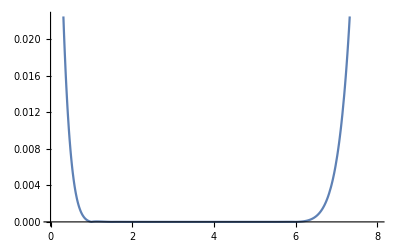

```mathematica
Clear[g1];
g1 = Plot[Er[x], {x, 0, 8}]
```

Here we see that our points of greatest accuracy fall along the points that we used to generate our interpolating polynomial, and the error curve begins to lift off sharply once we are outside the [1, 6] range, so from this graph alone it would seem that as long as we are within this [1, 6] we can calculate anything accurately. I expected my next tests to disprove this after what we had seen in Lab 7, but when I graphed my f[x] and p[x] I received the following:

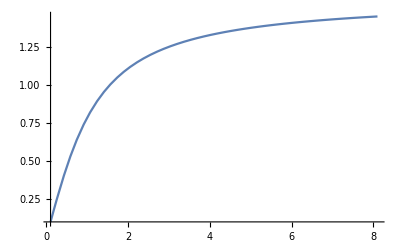

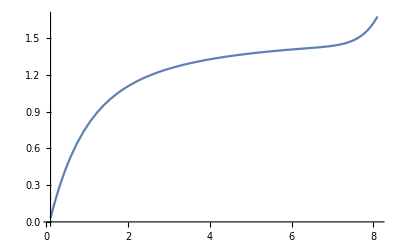

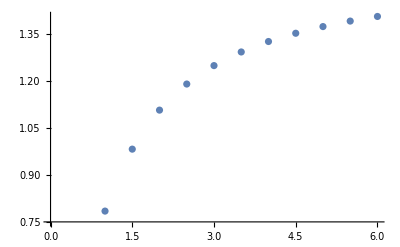

```mathematica
Clear[g2, g3, g4];
g2 = Plot[f[x], {x, 0.1, 8.1}]
g3 = Plot[p[x], {x, 0.1, 8.1}]
g4 = ListPlot[data1]
```

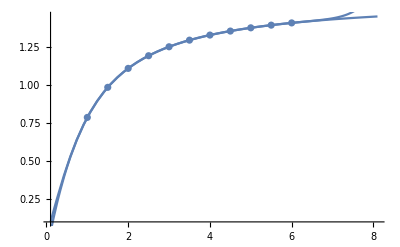

```mathematica
Show[g2, g3, g4]
```

We can see that the interpolating polynomial is pretty accurate up until we break out of the [1, 6] range, then it begins trailing off into more inaccurate values. We can conclude from this that the interpolating polynomial is very accurate when calculating for values within the specified x range, but the further one goes off outside of that range the more wild and inaccurate our approximations become.

## 4.1 CE # 11

Use Mathematica to find an interpolation polynomial for the points (0, 0), (1, 1), (2, 2.001), (3, 3), (4, 4), (5, 5). Evaluate the polynomial at the point x = 14 or x =20 to show that slight roundoff errors in the data can lead to suspicious results in extrapolation.

```mathematica
Clear[data1, data2, p, q];
data1 ={{0, 0}, {1, 1}, {2, 2.001}, {3, 3}, {4, 4}, {5, 5}};
p[x_] = Simplify[newtonForm[data1]]
p[20]
```

x (0.995+0.00891667 x-0.00491667 x^2+0.00108333 x^3-0.0000833333 x^4)

-109.2

This test goes to show just how inaccurate the interpolating polynomial can become even with just very slight roundoff errors. Had the point (2, 2.001) been (2, 2), then our interpolating polynomial would have correctly calculated f(x) = 20 when x = 20, as shown below:

```mathematica
data2 ={{0, 0}, {1, 1}, {2, 2}, {3, 3}, {4, 4}, {5, 5}};
q[x_] = Simplify[newtonForm[data2]]
q[20]
```

x

20

Simply by not rounding f(2) = 2.001 to f(2) = 2, we have gone from f(20) = 20 to f(20) = -109.2, which is an obscenely suspicious output given the trend established in the first 5 points. What are seemingly small roundoff errors can ultimately become a very destructive force for the accuracy and efficacy of your interpolating polynomial.

## 4.1 CE # 17

Find a rational function of the form

		g(x) = (a + bx)/(1 + cx)
		
that interpolates the function f(x) = arctan(x) at the points x_0 = 1,x_1 = 2, and x_2 = 3. On the same axes, plot the graphs of f and g.

Pade interpolation theory states that for two non-negative integers m and n, a Pade approximant [m/n] of a function f(x) is an approximation of f(x) by a rational function R(x), where R(x) = P(x)/Q(x) for polynomials of P(x) of order m and Q(x) of order n. Further, so long as we take the constant value of Q(x) to be 1, [m/n] is uniquely defined by f(x) and can be explicitly written as:

												[m/n] = (p_0 + p_1 x + p_2 x^2+...+ p_m x^m)/(1 + q_1 x + q_2 x^2+...+q_n x^n)
												
For my functions p(x) and q(x) I will create two different linear interpolation equations as per the form of g[x} (both numerator and denominator are linear equations).

```mathematica
Clear[p, q, f, g, data1];
f[x_] = ArcTan[x];

(* Data to be used in the construction of our divided differences table *)
data1 = Table[{i, f[i]}, {i, 1., 3.}];
MatrixForm[dividedDifference[data1]]
```

(0.785398 | 0 | 0
1.10715 | 0.321751 | 0
1.24905 | 0.141897 | -0.0899267)

From this we can extrapolate two different linear interpolation equations:

p(x) = 0.785398 + 0.321751(x - 1)
p_0 = 0.785398
p_1 = 0.321751

q(x) = 1.10715 + 0.141897(x - 1)
q_0 = 1
q_1 = 0.141897

so, 

P(x) = 0.785398 + 0.321751(x - 1)
Q(x) = 1 + 0.141897(x - 1)

And using our equation for [m/n]:

```mathematica
p[x_] = 0.785398 + 0.321751(x - 1);
q[x_] = 1 + 0.141897(x - 1);
Simplify[g[x_] = p[x] / q[x]]
```

(3.26749+2.2675 x)/(6.04737+1. x)

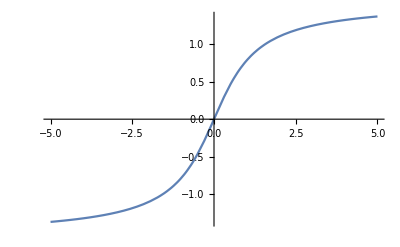

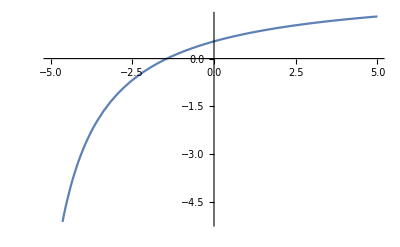

```mathematica
Clear[g1, g2];
g1 = Plot[f[x], {x, -5, 5}]
g2 = Plot[g[x], {x, -5, 5}]
```

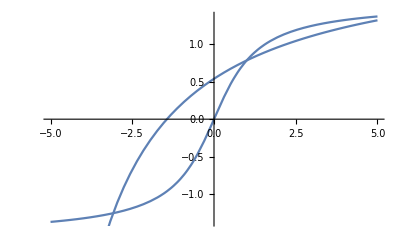

```mathematica
Show[g1, g2]
```

This seems like a pretty inaccurate approximation, but I believe I performed Pade interpolation properly. I suppose when considering that our g(x) is created from two linear functions then this approximation seems more accurate, given how extremely inaccurate the two linear functions are on their own. I would assume that using higher degree polynomials when creating the Pade interpolating polynomial will improve the accuracy of the resulting I.P.

## 4.2 # 1

Use a divided-difference table to show that the following data can be represented by a polynomial of degree 3:

								x | -2 | -1 | 0 | 1 | 2 | 3
y | 1 | 4 | 11 | 16 | 13 | -4
								
(I did this by hand to practice for the midterm)

In order to craft a polynomial of degree three, we need to go up to the 3rd degree term of our divided-difference table, which is

						f(x_i, x_(i+1), x_(i+2), x_(i+3))  = (f(x_(i+1), x_(i+2), x_(i+3)) - f(x_i, x_(i+1), x_(i+2)))/(x_(i+3) - x_i)
						
						where
						
						f(x_i, x_(i+1), x_(i+2))  = (f(x_(i+1), x_(i+2)) - f(x_i, x_(i+1)))/(x_(i+2) - x_i)
						
						and
						
						f(x_i, x_(i+1))  = (f(x_(i+1)) - f(x_i))/(x_(i+1) - x_i)
						
We should only need 4 points within x = [-2, 3], including the two endpoints x = -2 and x = 3. It is important to retain the endpoints because those dictate the range of x values for which f(x) can be accurately computed by this polynomial, if we were to only use the range [-2, 2] rather than [-2, 3], then we would not be able to accurately calculate for x = 3.

								x | x_0 = -2 | x_1 = -1 | x_2 = 1 | x_3 = 3
y | f(x_0) = 1 | f(x_1) = 4 | f(x_2)  = 16 | f(x_3) = -4
								
f(x_0, x_1):
f(-2, -1) = (4 - 1) / (-1 + 2) = 3

f(x_1, x_2):
f(-1, 1) = (16 - 4) / (1 + 1) = 6

f(x_2, x_3):
f(1, 3) = (-4 - 16) / (3 - 1) = -10

f(x_0, x_1, x_2):
f(-2, -1, 1) = (6 - 3) / (1 + 2) = 1

f(x_1, x_2, x_3):
f(-1, 1, 3) = (-10 - 6) / (3 + 1) = -4

f(x_0, x_1, x_2, x_3):
f(-2, -1, 1, 3) = (-4 - 1) / (3 + 2) = -1

Now we can construct our divided differences table:

						x | f(x) | f(x_i, x_(i+1)) | f(x_i, x_(i+1), x_(i+2)) | f(x_i, x_(i+1), x_(i+2), x_(i+3))
-2 | 1 |   |   |  
-1 | 4 | 3 |   |  
1 | 16 | 6 | 1 |  
3 | -4 | 10 | -4 | -1
						
We can construct an interpolation polynomial in Newton’s form from the divided difference table using the following equation:
						
P_n(x) = f[x_0] + f[x_0, x_1](x - x_0) + f[x_0, x_1, x_2](x - x_0)(x - x_1) + ... + f[x_0, x_1, x_2, ... , x_n](x - x_0)(x - x_1) ... (x - x_(n - 1))
						
This means that our third degree interpolation polynomial is:

P_3(x) = 1 + 3(x + 2) + (x + 2)(x + 1) - (x + 2)(x + 1)(x - 1)

First lets confirm that this is indeed a degree 3 polynomial:

```mathematica
Clear[p];
p[x_] = 1 + 3(x + 2) + (x + 2)(x + 1) - (x + 2)(x + 1)(x - 1);
Simplify[p[x]]
```

11+7 x-x^2-x^3

And now we can confirm that this polynomial encodes all of our data by plugging in all of our inputs and checking if we receive the expected outputs:

```mathematica
p[-2]
p[-1]
p[0]
p[1]
p[2]
p[3]
```

1

4

11

16

13

-4

We see that we get the expected outputs even for values not used in the creation in the polynomial, which confirms that this polynomial encodes all the data.

## 4.2 # 6

How accurately can we determine sin(x) by linear interpolation, given a table of sin(x) to ten decimal places, for x in [0, 2] with h = 0.01?

We know that the function sin(x) is continuous on [0, 2], and we know that for all | f^(n + 1)(x)| ≦ 1. Thus, we can use theorem 2 from the textbook, which says:

															|f(x) - p(x)|  ≦ 1/(4(n + 1))Mh^(n+1)
															
using f(x) = sin(x), M = 1, h = 0.01, and since this is a linear interpolating function we use n = 1, which comes out to:

```mathematica
(1/8)*(0.01^2)
```

0.0000125

So we are capable of determining sin(x) via linear interpolation with an accuracy of of 1.25 x 10^-5.

## 4.2 # 7

(Continuation) Given the data

								x | sin(x) | cos(x)
0.70 | 0.6442176872 | 0.7648421837
0.71 | 0.6518337710 | 0.7583618760
								
find approximate values of sin(0.705) and cos(0.702) by linear interpolation. What is the error?

```mathematica
Clear[f, g];
(* Data points for generating linear interpolating funciton of sin(x) *)
Sdata = {{0.70, 0.6442176872}, {0.71, 0.6518337710}};
(* Data points for generating linear interpolating funciton of cos(x) *)
Cdata = {{0.70, 0.7648421837}, {0.71, 0.7583618760}};

(* Linear interpolating function for sin(x) *)
f[x_] = Simplify[newtonForm[Sdata]];
(* Linear interpolating function for cos(x) *)
g[x_] = Simplify[newtonForm[Cdata]];

(* Caluclation for sin(0.705) *)
f[0.705]
(* Calculation for cos(0.702) *)
g[0.702]
```

0.648026

0.763546

```mathematica
(* Error calculation on f(0.705) *)
Serror = Abs[Sin[0.705] - f[0.705]]
(* Error calculation on g(0.702) *)
Cerror = Abs[Cos[0.702] - g[0.702]]
```

8.10044×10^-6

6.10093×10^-6

## 4.2 # 8

Linear interpolation in a table of function values means the following: If y_0 = f(x_0) and y_1 = f(x_1) are tabulated values, and if x_0 < x < x_1, then an interpolated value of f(x) is y_0 + [(y_1 - y_0) / (x_1 -x_0)](x - x_0), as explained at the beginning of Section 4.1. A table of values of cos(x) is required so that the linear interpolation will yield five-decimal-place accuracy (10^-5) for any value of x in [0, π]. Assume that the tabular values are equally spaced, and determine the minimum number of entries needed in this table.

I approached this in somewhat of a brute force manner. I wrote the skeleton for all the code I was going to need, and then I simply increased the size of my data1 table until I had enough values to calculate for anything in [0, π] with five-decimal-place accuracy.

```mathematica
Clear[data1, data2, f, g, p];
f[x_] = N[Cos[x], 5];

(* I started with Table[{i, f[i], {i, 0, Pi}] to see if I could acheive my goal by just using the most minimum points available *)
data1 = Table[{i, f[i]}, {i, 0., Pi}]
```

{{0.,1.},{1.,0.540302},{2.,-0.416147},{3.,-0.989992}}

```mathematica
(* Now we can create the interpolated value f(x) = Subscript[y, 0] + [(Subscript[y, 1] - Subscript[y, 0]) / (Subscript[x, 1] - Subscript[x, 0])](x - Subscript[x, 0]) with Subscript[y, 0] = 1, Subscript[x, 0] = 0, Subscript[y, 1] = 0.540302, Subscript[x, 1] = 1 *)
g[x_] = N[1 + ((0.5403023058681398  - 1)/(1))(x), 5];
data2 = MatrixForm[Table[{i, f[i],  g[i]}, {i, 0., Pi}]]
```

(0. | 1. | 1.
1. | 0.540302 | 0.540302
2. | -0.416147 | 0.0806046
3. | -0.989992 | -0.379093)

So we are pretty close just from this first attempt as we have matched one output, but we are going to need more values to further improve the approximation of our values. Lets attempt to double the size of our data1 table and see if we can improve the accuracy with twice as many terms:

```mathematica
Clear[data1, data2, f, g, p];
f[x_] = N[Cos[x], 5];

data1 = Table[{.5i, f[.5i]}, {i, 0., 2Pi}]
```

{{0.,1.},{0.5,0.877583},{1.,0.540302},{1.5,0.0707372},{2.,-0.416147},{2.5,-0.801144},{3.,-0.989992}}

```mathematica
(* Now we can create the interpolated value f(x) = Subscript[y, 0] + [(Subscript[y, 1] - Subscript[y, 0]) / (Subscript[x, 1] - Subscript[x, 0])](x - Subscript[x, 0]) with Subscript[y, 0] = 1, Subscript[x, 0] = 0, Subscript[y, 1] = 0.877583, Subscript[x, 1] = 0.5 *)
g[x_] = N[1 + ((0.877583 - 1)/(0.5))(x), 5];
data2 = MatrixForm[Table[{.5i, f[.5i], g[.5i]}, {i, 0., 2Pi}]]
```

(0. | 1. | 1.
0.5 | 0.877583 | 0.877583
1. | 0.540302 | 0.755166
1.5 | 0.0707372 | 0.632749
2. | -0.416147 | 0.510332
2.5 | -0.801144 | 0.387915
3. | -0.989992 | 0.265498)

Now I am a bit stumped, because it seems that by increasing the number of points used to create our linear function we haven’t actually improved our approximation at all, in fact our approximation for x = 1, x =2, and x =3 have actually gotten worse. So far all I have been able to do is accurately calculate  just the first term. I am going to try once more using this method, and double the number of points again.

```mathematica
Clear[data1, data2, f, g, p];
f[x_] = N[Cos[x], 5];

data1 = Table[{.25i, f[.25i]}, {i, 0., 4Pi}]
```

{{0.,1.},{0.25,0.968912},{0.5,0.877583},{0.75,0.731689},{1.,0.540302},{1.25,0.315322},{1.5,0.0707372},{1.75,-0.178246},{2.,-0.416147},{2.25,-0.628174},{2.5,-0.801144},{2.75,-0.924302},{3.,-0.989992}}

```mathematica
(* Now we can create the interpolated value f(x) = Subscript[y, 0] + [(Subscript[y, 1] - Subscript[y, 0]) / (Subscript[x, 1] - Subscript[x, 0])](x - Subscript[x, 0]) with Subscript[y, 0] = 1, Subscript[x, 0] = 0, Subscript[y, 1] = 0.877583, Subscript[x, 1] = 0.5 *)
g[x_] = N[1 + ((0.9689124217106447 - 1)/(0.25))(x), 5];
data2 = MatrixForm[Table[{.25i, f[.25i], g[.25i]}, {i, 0., 4Pi}]]
```

(0. | 1. | 1.
0.25 | 0.968912 | 0.968912
0.5 | 0.877583 | 0.937825
0.75 | 0.731689 | 0.906737
1. | 0.540302 | 0.87565
1.25 | 0.315322 | 0.844562
1.5 | 0.0707372 | 0.813475
1.75 | -0.178246 | 0.782387
2. | -0.416147 | 0.751299
2.25 | -0.628174 | 0.720212
2.5 | -0.801144 | 0.689124
2.75 | -0.924302 | 0.658037
3. | -0.989992 | 0.626949)

So yet again this method has not succeeded in producing a linear interpolating function that can accurately compute everything in [0, Pi].  Since this has been failing me, I decided to try to use a divided differences table to see if I couldn’t come up with a linear function that encodes all of [0, Pi].

```mathematica
Clear[data1, data2, f, g, p];
f[x_] = N[Cos[x], 5];
data1 = Table[{i, f[i]}, {i, 0., Pi}];
MatrixForm[dividedDifference[data1]]
```

(1. | 0 | 0 | 0
0.540302 | -0.459698 | 0 | 0
-0.416147 | -0.956449 | -0.248376 | 0
-0.989992 | -0.573846 | 0.191302 | 0.146559)

```mathematica
p[x_] = 1 - 0.45969769413186023(x);
data2 = MatrixForm[Table[{i, f[i], p[i]}, {i, 0., Pi}]]
```

(0. | 1. | 1.
1. | 0.540302 | 0.540302
2. | -0.416147 | 0.0806046
3. | -0.989992 | -0.379093)

I haven’t displayed every single attempt at this method, but I have attempted it enough times to say that it, too, is not working for creating this linear equation. I have gone back to my original method and attempted that a few more times with increasingly bigger tables of cos(x) values and the trend has remained the same, the more points I use, the less accurate my calculations become. I can’t decrease the number of points I use because then I run the risk of not being able to accurately calculate anything outside my range of x values, so for the time being I find myself stumped at this question.

## 4.2 # 17

Find a polynomial p that takes these values: p(1) = 3, p(2) = 1, p(0) = -5. You may use any method you wish. You may leave the polynomial in any convenient form, not necessarily the standard form, (Σ_(k = 1))^nc_kx^k. Next, find a new polynomial q that takes those same three values and q(3) = 7.

```mathematica
Clear[data1, data2];

(* Data set for computing the lowest-degree polynomial with three points *)
data1 = {{1, 3}, {2, 1}, {0, -5}};
(* Data set for computing the lowest-degree polynomial with three points *)
data2 = {{1, 3}, {2, 1}, {0, -5}, {3, 7}};

(* Use InterpolatingPolynomial to find the first polynomial representation *)
Simplify[InterpolatingPolynomial[data1, x]]
(* Use newtonForm (to change things up) to find the second polynomial representation *)
Simplify[newtonForm[data2]]
```

-5+13 x-5 x^2

-5+19 x-14 x^2+3 x^3